Note that the initial values for these fits are typically generated using Levy’s Method (see Matlab Code in fitting_v1.m and levy_estimation.m). While this isn’t always amazingly accurate, it does provide a consistent method for coming up with the initial parameter guesses.

The output from the Matlab residue function is used to populate a_p (poles) and c_p (residues) initial guesses.

## Import Data:

#### Remove points outside our range of interest:

```mathematica
Clear[auData,agData,alData,cuData,siData,siO2Data,auPts,agPts,alPts,cuPts,siPts,siO2Pts, λmin,λmax]
λmin=0.3; (* μm *)
λmax=1.3;
(* Format is wavelength (μm), n, k *)
auData = Import[FileNameJoin[{NotebookDirectory[], "Au-JC.txt"}],"Data"];
agData = Import[FileNameJoin[{NotebookDirectory[], "Ag-JC.txt"}],"Data"];
alData = Import[FileNameJoin[{NotebookDirectory[], "Al-Cheng.txt"}],"Data"];
cuData = Import[FileNameJoin[{NotebookDirectory[], "Cu-JC.txt"}],"Data"];
siData = Import[FileNameJoin[{NotebookDirectory[], "Si-Green.txt"}],"Data"];
auPts=Select[auData,λmin≤#[[1]]≤λmax&];
agPts=Select[agData,λmin≤#[[1]]≤λmax&];
alPts=Select[alData,λmin≤#[[1]]≤λmax&];
cuPts=Select[cuData,λmin≤#[[1]]≤λmax&];
siPts=Select[siData,λmin≤#[[1]]≤λmax&];
```

## Convert to ϵ_r and ϵ_i (and eV from λ):

```mathematica
Clear[auEps,agEps,alEps,cuEps,speedC,siEps,epsFunc,h]
speedC=2.99792458*10^14; (* in μm/sec *)
h=4.135667*10^-15; (* eV sec *)
epsFunc[data_]:=Table[{h*speedC/data[[i,1]],data[[i,2]]^2-data[[i,3]]^2+2 ⅈ data[[i,2]] data[[i,3]]},{i,1,Length[data]}]; (* eV *)
auEps=epsFunc[auPts];
agEps=epsFunc[agPts];
alEps=epsFunc[alPts];
cuEps=epsFunc[cuPts];
siEps=epsFunc[siPts];
```

## Critical-Point Fitting:

### Fitting Function:

```mathematica
Clear[cpFunc,cIm,cRe,aIm,aRe,σ,eInf,errorFunc]
cpFunc[ω_,aRe_,aIm_,cRe_,cIm_]:=(cRe+ⅈ*cIm)/(-ⅈ ω - (aRe+ⅈ aIm))+(cRe-ⅈ cIm)/(-ⅈ ω - (aRe-ⅈ aIm));
errorFunc[fit_,model_,data_]:=Sum[
Sqrt[Abs[
data[[i,2]]-model[data[[i,1]]]/.fit 
]],
{i,1,Length[data]}];
```

### Plotting Function:

```mathematica
Clear[plotFunc,model]
plotFunc[fit_,model_,data_]:=
Show[
Plot[{
Tooltip[Re[model[ω]]/.fit,"Re[ϵ_r]"],
Tooltip[Im[model[ω]]/.fit,"Im[ϵ_r]"]},
{ω,speedC*h/(λmax),speedC*h/(λmin)},PlotLegends->{"Real","Imaginary"},PlotRange->All],ListPlot[{
Re[data],
Table[{data[[i,1]],Im[data[[i,2]]]},{i,1,Length[data]}]
},PlotRange->All]
]
```

### Output formatting:

```mathematica
Clear[outputFunc,model,fit]
outputFunc[model_, fit_,n_]:=Partition[Flatten[
{
{"ϵ_∞",eInf},{"σ",σ},
Partition[Riffle[
Table[{StringForm["a_(``)",i],aRe@i+ⅈ aIm@i},{i,n}],
Table[{StringForm["c_(``)",i],cRe@i+ⅈ cIm@i}, {i,n}]
],2]
}
],2]/.fit//TableForm;
```

### Fits for Individual Metals:

#### Shared Constraints:

```mathematica
Clear[shareCons]
shareCons={eInf≥1,σ≥0};
```

#### Al:

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (10).

263.339

ϵ_∞ | 1.
σ | 413.505
a_(RowBox[{) | -0.272493+1.44484 ⅈ
a_(RowBox[{) | -0.116623+0.133088 ⅈ
c_(RowBox[{) | 3.80577-5.88315 ⅈ
c_(RowBox[{) | -209.786-295.234 ⅈ

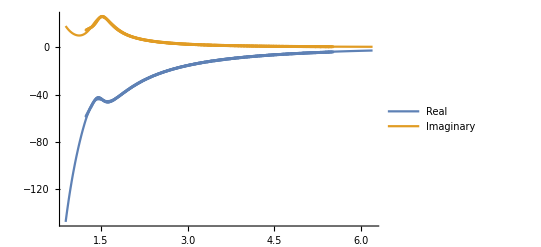

```mathematica
Clear[aRe,aIm,cRe,cIm,σ,n,eInf,params,model,constraints,aData,ϕData,ΩData,ΓData,fit,aReEst,aImEst,cReEst,cImEst]
n=2;
data=alEps;

(* Initial conditions for the fit. Can be highly sensitive *)
aReEst={0.2548,0.2548,-1.55,1};
aImEst = {1.7122,-1.7122,13};
cReEst={1.3397,1.3397,7,1};
cImEst={-2.4896,2.4896,10};
σEst=1000;
eInfEst = 1.0;

params=Flatten[Table[{{aRe@i,aReEst[[i]]},{aIm@i,aImEst[[i]]},{cRe@i,cReEst[[i]]},{cIm@i,cImEst[[i]]}},{i,n}],1];
params=Union[params,{{eInf,eInfEst},{σ,σEst}}];
model[ω_]:=eInf+σ/(-ⅈ  ω)+Sum[cpFunc[ω,aRe@i,aIm@i,cRe@i,cIm@i],{i,n}]; 
modelCons=Flatten[{model[ω],shareCons}];
fit=FindFit[data,modelCons,params,ω,NormFunction->(Norm[Abs[#]] &),Method->NMinimize,WorkingPrecision->10];
rmserr=errorFunc[fit,model,data]
outputFunc[model,fit,n]
plotFunc[fit,model,data]
```

#### Au:

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (10).

26.0571

ϵ_∞ | 1.
σ | 5.19039
a_(RowBox[{) | -0.994406+2.45951 ⅈ
a_(RowBox[{) | -0.0219569+0.224007 ⅈ
c_(RowBox[{) | 7.01819-0.31594 ⅈ
c_(RowBox[{) | -0.67478-155.767 ⅈ

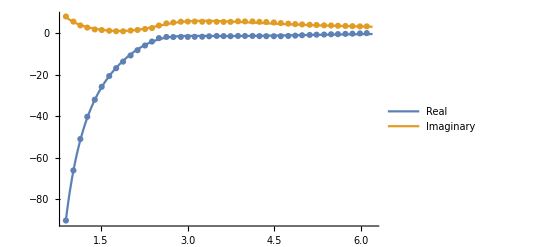

```mathematica
Clear[aRe,aIm,cRe,cIm,σ,n,eInf,params,model,constraints,aData,ϕData,ΩData,ΓData,fit,aReEst,aImEst,cReEst,cImEst,data,interp,rmserr]
n=2;
data=auEps;

(* Initial conditions for the fit. Can be highly sensitive *)
aReEst={1.06123,0.402315,-1.55,1};
aImEst = {4.52658,1.605786,13};
cReEst={1.37642,4.710889,7,1};
cImEst={0.560685,5.191185,10};
σEst=50;
eInfEst = 1.7;

params=Flatten[Table[{{aRe@i,aReEst[[i]]},{aIm@i,aImEst[[i]]},{cRe@i,cReEst[[i]]},{cIm@i,cImEst[[i]]}},{i,n}],1];
params=Union[params,{{eInf,eInfEst},{σ,σEst}}];
model[ω_]:=eInf+σ/(-ⅈ  ω)+Sum[cpFunc[ω,aRe@i,aIm@i,cRe@i,cIm@i],{i,n}];
modelCons=Flatten[{model[ω],shareCons}];
fit=FindFit[data,modelCons,params,ω,NormFunction->(Norm[Abs[#]] &),Method->NMinimize,WorkingPrecision->10];
rmserr=errorFunc[fit,model,data]
outputFunc[model,fit,n]
plotFunc[fit,model,data]
```

#### Ag:

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (10).

11.7849

ϵ_∞ | 2.53778
σ | 7.34706
a_(RowBox[{) | -0.00238268-0.166134 ⅈ
c_(RowBox[{) | -3.17139+246.321 ⅈ
a_(RowBox[{) | -0.393139+4.27188 ⅈ
c_(RowBox[{) | 0.945098-1.37423 ⅈ

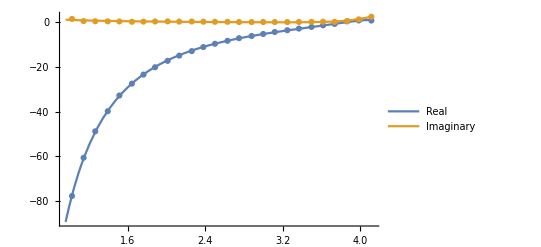

```mathematica
Clear[aRe,aIm,cRe,cIm,σ,n,eInf,params,model,constraints,aData,ϕData,ΩData,ΓData,fit,aReEst,aImEst,cReEst,cImEst]
n=2;
data=agEps;

(* Initial conditions for the fit. Can be highly sensitive *)
aReEst={-0.967,-2.513,-1.07,1};
aImEst = {6.26,3.92,3.96,1.0};
cReEst={-1.08,0.28247,3.6945,1};
cImEst={9.0177,0.333,-0.716};
σEst=2500;
eInfEst = 1.0;

params=Flatten[Table[{{aRe@i,aReEst[[i]]},{aIm@i,aImEst[[i]]},{cRe@i,cReEst[[i]]},{cIm@i,cImEst[[i]]}},{i,n}],1];
params=Union[params,{{eInf,eInfEst},{σ,σEst}}];
model[ω_]:=eInf+σ/(-ⅈ  ω)+Sum[cpFunc[ω,aRe@i,aIm@i,cRe@i,cIm@i],{i,n}]; 
modelCons=Flatten[{model[ω],shareCons}];
fit=FindFit[data,modelCons,params,ω,NormFunction->(Norm[Abs[#]] &),Method->NMinimize,WorkingPrecision->10,MaxIterations->1000]; (* Ag was much more sensitive to number of iterations than othe materials for some reason *)
rmserr=errorFunc[fit,model,data]
outputFunc[model,fit,n]
plotFunc[fit,model,data]
```

#### Cu:

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (10).

20.2926

ϵ_∞ | 1.98801
σ | 27.8466
a_(RowBox[{) | -0.607993+2.0456 ⅈ
a_(RowBox[{) | -0.0173655-0.134845 ⅈ
c_(RowBox[{) | 3.84516+1.37118 ⅈ
c_(RowBox[{) | -9.84239+261.159 ⅈ

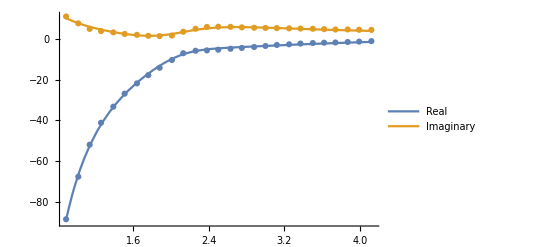

```mathematica
Clear[aRe,aIm,cRe,cIm,σ,n,eInf,params,model,constraints,aData,ϕData,ΩData,ΓData,fit,aReEst,aImEst,cReEst,cImEst]
n=2;
data=cuEps;

(* Initial conditions for the fit. Can be highly sensitive *)
aReEst={0.55057,-0.1428,-1.55,1};
aImEst = {5.258,1.4076,13};
cReEst={0.569,-3.39,7,1};
cImEst={0.7458,3.1855,10};
σEst=10;
eInfEst = 1.0;

params=Flatten[Table[{{aRe@i,aReEst[[i]]},{aIm@i,aImEst[[i]]},{cRe@i,cReEst[[i]]},{cIm@i,cImEst[[i]]}},{i,n}],1];
params=Union[params,{{eInf,eInfEst},{σ,σEst}}];
model[ω_]:=eInf+σ/(-ⅈ  ω)+Sum[cpFunc[ω,aRe@i,aIm@i,cRe@i,cIm@i],{i,n}]; 
modelCons=Flatten[{model[ω],shareCons}];
fit=FindFit[data,modelCons,params,ω,NormFunction->(Norm[Abs[#]] &),Method->NMinimize,WorkingPrecision->10];
rmserr=errorFunc[fit,model,data]
outputFunc[model,fit,n]
plotFunc[fit,model,data]
```

#### Si:

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (10).

19.871

ϵ_∞ | 1.30676
σ | 0.0471157
a_(RowBox[{) | -0.116424+3.3587 ⅈ
a_(RowBox[{) | -0.381842+4.26879 ⅈ
a_(RowBox[{) | -0.37732-3.6481 ⅈ
c_(RowBox[{) | 1.96042-2.20821 ⅈ
c_(RowBox[{) | -0.578006-13.8223 ⅈ
c_(RowBox[{) | 1.38221+4.59924 ⅈ

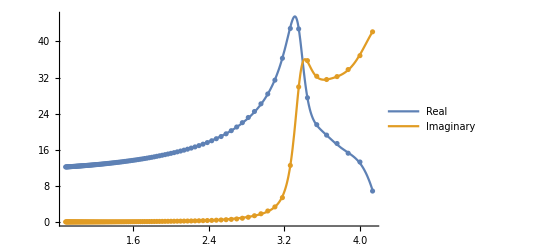

```mathematica
Clear[aRe,aIm,cRe,cIm,σ,n,eInf,params,model,constraints,aData,ϕData,ΩData,ΓData,fit,aReEst,aImEst,cReEst,cImEst]
n=3;
data=siEps;

(* Initial conditions for the fit. Can be highly sensitive *)
aReEst={0.197295,0.6591,0.145914,1};
aImEst = {4.3585,4.043958,3.36746};
cReEst={0.033185,-0.064121,-0.028795,1};
cImEst={0.026843,0.14079,0.02895};
σEst=10;
eInfEst = 1.0;

params=Flatten[Table[{{aRe@i,aReEst[[i]]},{aIm@i,aImEst[[i]]},{cRe@i,cReEst[[i]]},{cIm@i,cImEst[[i]]}},{i,n}],1];
params=Union[params,{{eInf,eInfEst},{σ,σEst}}];
model[ω_]:=eInf+σ/(-ⅈ  ω)+Sum[cpFunc[ω,aRe@i,aIm@i,cRe@i,cIm@i],{i,n}]; 
modelCons=Flatten[{model[ω],shareCons}];
fit=FindFit[data,modelCons,params,ω,NormFunction->(Norm[Abs[#]] &),Method->NMinimize,WorkingPrecision->10];
rmserr=errorFunc[fit,model,data]
outputFunc[model,fit,n]
plotFunc[fit,model,data]
```